```mathematica
u=(0.9702989999999999-3.9105989999999995 ⅇ^(ⅈ ξ)+5.910299999999999 ⅇ^(2 ⅈ ξ)-3.9699999999999998 ⅇ^(3 ⅈ ξ)+ⅇ^(4 ⅈ ξ))/(d+(0.029551916666666678-3 d) ⅇ^(ⅈ ξ)+(-0.059401333333333486+3 d) ⅇ^(2 ⅈ ξ)+(0.029850416666666803-d) ⅇ^(3 ⅈ ξ));
```

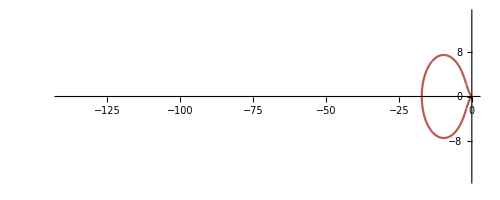

```mathematica
d=-0.1;
p1=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.73,0.37,0.31]
,AxesOrigin->{0,0}
,PlotRange->{{-140,0},{-15,15}}]
```

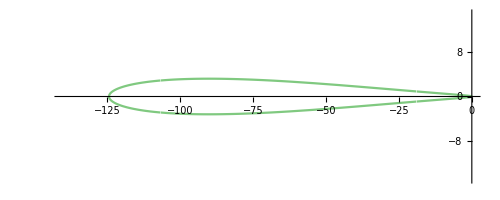

```mathematica
d=-0.001;
p2=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.5,0.79,0.5]
,AxesOrigin->{0,0}
,PlotRange->{{-140,0},{-15,15}}]
```

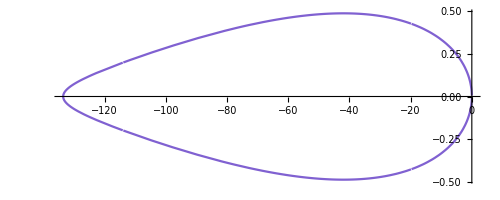

```mathematica
d=0.0001;
p3=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.5,0.38,0.82]
,AxesOrigin->{0,0}
,PlotRange->All]
```

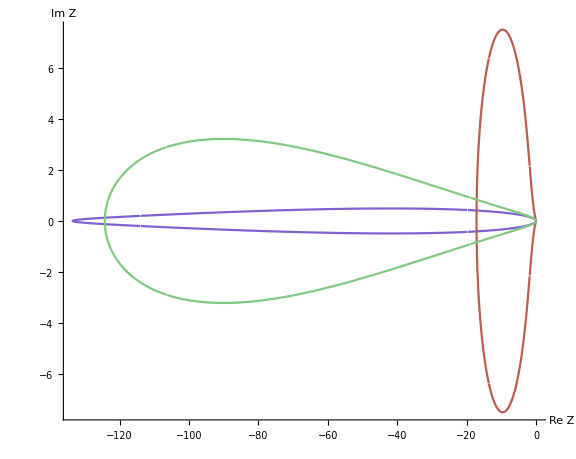

```mathematica
Show[p3,p1,p2,ImageSize->Large,LabelStyle->{14,GrayLevel[0]},Axes->True,AxesLabel->{HoldForm[Re Z],HoldForm[Im Z]},SetOptions[Plot,AspectRatio->0.8]]
```